```mathematica
ClearAll["Global`*"]
```

## Question C.1 (replacing random pairs of edges)

```mathematica
getGraph[AA_,J_]:={A0=AA;
For[j=1,j≤J,j++,edges=Position[A0,1];
s1=Random[Integer,{10,40}];
s2=Random[Integer,{10,40}];
e1=edges[[s1]];
e2=edges[[s2]];
en1={e1[[1]],e2[[2]]};
en2={e2[[1]],e1[[2]]};
If[(e1[[1]]-e2[[2]])*(e2[[1]]-e1[[2]])==0, ,If[MemberQ[edges,en1], ,If[MemberQ[edges,en2], ,{Anext=ReplacePart[A0,0,e1];
Anext=ReplacePart[Anext,0,e2];
Anext=ReplacePart[Anext,0,Reverse[e1]];
Anext=ReplacePart[Anext,0,Reverse[e2]];
Anext=ReplacePart[Anext,1,Reverse[en1]];
Anext=ReplacePart[Anext,1,Reverse[en2]];
Anext=ReplacePart[Anext,1,en1];
Anext=ReplacePart[Anext,1,en2]}
]]];
A0=Anext];Aout=A0}[[1]]
```

```mathematica
AA={{0, 1, 1, 1, 1, 1, 1,1, 1, 1},
{1, 0, 1, 1, 1, 1, 0, 0, 0, 0},
{1, 1, 0, 1, 1, 1, 0, 0, 0, 0},
{1, 1, 1, 0, 1, 0, 0, 0, 0, 0},
{1, 1, 1, 1, 0, 0, 0, 0, 0, 0},
{1, 1, 1, 0, 0, 0, 0, 0, 0, 0},
{1, 0, 0, 0, 0, 0, 0, 1, 1, 0},
{1, 0, 0, 0, 0, 0, 1, 0, 0, 1},
{1, 0, 0, 0, 0, 0, 1, 0, 0, 0},
{1, 0, 0, 0, 0, 0, 0, 1, 0, 0}};
```

```mathematica
AA1=getGraph[AA,1]
```

{{0,1,1,1,1,1,1,1,1,1},{1,0,1,1,1,1,0,0,0,0},{1,1,0,1,0,1,0,1,0,0},{1,1,1,0,1,0,0,0,0,0},{1,1,0,1,0,0,1,0,0,0},{1,1,1,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,1},{1,0,0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,1,0,0}}

```mathematica
AA1-AA//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Norm[AA1-AA]
```

2

```mathematica
Norm[AA]//N
```

4.73204

## Question C.2 (building a bigger aggregated graph)

```mathematica
J=2; (* number of iteration *)
AA0=AA;
nv=Length[AA0];
NA=Norm[AA0];
AAC=Table[{},{i,J+1}]; (* collection *)
AG0=AA0;
AAC[[1]]=AA0;
r=1;
For[j1=1,j1<=J,j1++,
AA0=getGraph[AA0,1];
AAC[[j1+1]]=AA0;
AG1=ConstantArray[0,{(j1+1) nv,(j1+1) nv}];
AG1[[1;;j1 nv,1;;j1 nv]]=AG0;
vAG0=RandomChoice[(Total[AG0]/Total[AG0,2])^r-> Table[i,{i,Length[AG0]}]];
AG1[[j1 nv+1;;(j1+1) nv,j1 nv+1;;(j1+1) nv]]=AA0;
vAA0=RandomChoice[(Total[AA0]/Total[AA0,2])^r-> Table[i,{i,Length[AA0]}]]+Length[AG0];
AG0=AG1;
AG0[[vAG0,vAA0]]=1;
AG0[[vAA0,vAG0]]=1;
];
```

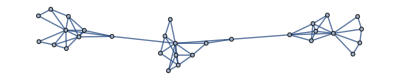

```mathematica
AdjacencyGraph[AG0]
```